```mathematica
ParametricPlot3D[{Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ],Sin[ϕ]},{θ,-4,4},{ϕ,-4,4}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t,t^2,t^3},{t,-20,20},PlotRange-> {{-5,5},{-5,5},{-5,5}},PlotPoints->100]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x*t,x*t^2,x*t^3},{t,-20,20},{x,-10,10},PlotRange-> {{-5,5},{-5,5},{-5,5}},PlotPoints->300]
```

-Graphics3D-

```mathematica
ContourPlot3D[{y*y==x*z},{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
Eigenvalues[{{0,0,1/2},{0,-1,0},{1/2,0,0}}]
```

{-1,-1/2,1/2}

```mathematica
ParametricPlot3D[{r*(1+Sin[θ]),r*Cos[θ],r*(1-Sin[θ])},{r,-20,20},{θ,-10,10},PlotRange-> {{-5,5},{-5,5},{-5,5}}]
```

-Graphics3D-

```mathematica
Plot3D[x^2-y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{x^2-y^2,2x-2y},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[x^2+y^2],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2+y^2],x/Sqrt[2]-y/Sqrt[2]},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[x*y/(x^2+y^2),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[(x^2*y)/(x^6+y^2),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
D[{(x^2*y)/(x^2+y^2)},x]
D[{(x^2*y)/(x^2+y^2)},y]
```

{-(2 x^3 y)/((x^2+y^2)^2)+(2 x y)/(x^2+y^2)}

{-(2 x^2 y^2)/((x^2+y^2)^2)+x^2/(x^2+y^2)}

```mathematica
Plot3D[(x^2*y)/(x^2+y^2),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
D[{x*y,x^2-y^2},y]
```

{x,-2 y}

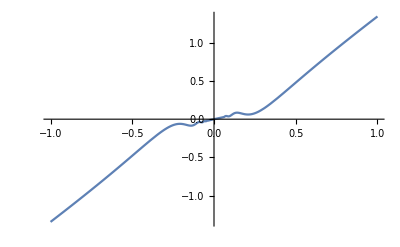

```mathematica
Plot[x/2+x^2*Sin[1/x],{x,-1,1}]
```

```mathematica
D[x/2+(x^2*Sin[1/x]),{x,0}]
```

x/2+x^2 Sin[1/x]

```mathematica
Limit[h*Sin[1/h],h->0]
```

0

```mathematica
D[{(x/2)+(x^2*Sin[1/x])},x]
```

{1/2-Cos[1/x]+2 x Sin[1/x]}

```mathematica
f[x_,y_]=ϕ[(x+y)/(x-y)];
D[f[x,y],x]
```

(2 (x+y))/(x-y)^2-(2 (x+y)^2)/(x-y)^3

```mathematica
x*(D[(x+y)/(x-y),x])+y*(D[(x+y)/(x-y),y])
```

x (1/(x-y)-(x+y)/(x-y)^2)+y (1/(x-y)+(x+y)/(x-y)^2)

```mathematica
y*(D[(x+y)/(x-y),y])
```

y (1/(x-y)+(x+y)/(x-y)^2)

```mathematica
D[x/y,y]
```

-x/y^2

```mathematica
D[x/2+x^2*Sin[1/x],x]
```

1/2-Cos[1/x]+2 x Sin[1/x]

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

```mathematica
Limit[(h/2+h^2*Sin[1/h])/h,h->0]
```

1/2

```mathematica
D[{x*y,x^2-y^2},x]
```

{y,2 x}

```mathematica
D[{x*y,x^2-y^2},y]
```

{x,-2 y}

```mathematica
MatrixForm[D[{(x1-x2)^2+(y1-y2)^2+(z1-z2)^2-4,(x1-1)^2+y1^2+z1^2-1,(x2+1)^2+y2^2+z2^2-1},{{x1,y1,z1,x2,y2,z2},1}]]
```

(2 (x1-x2) | 2 (y1-y2) | 2 (z1-z2) | -2 (x1-x2) | -2 (y1-y2) | -2 (z1-z2)
2 (-1+x1) | 2 y1 | 2 z1 | 0 | 0 | 0
0 | 0 | 0 | 2 (1+x2) | 2 y2 | 2 z2)

General::ivar: 1 is not a valid variable.

```mathematica
D[{Cos[t],Sin[t],t},t]
```

{-Sin[t],Cos[t],1}

```mathematica
ParametricPlot3D[{{Cos[t],Sin[t],t},{u*-Sin[t]+Cos[t],u*Cos[t]+Sin[t],u+t}},{t,-20,20},{u,-10,10}]
ParametricPlot3D[{u*-Sin[t]+Cos[t],u*Cos[t]+Sin[t],u+t},{t,4,4.01},{u,-10,10}]
```

-Graphics3D-

-Graphics3D-

```mathematica
D[{x*y-x+y+z^2},{{x,y,z},1}]
```

{{-1+y,1+x,2 z}}

```mathematica
D[{x*y-x+y+z^2},{z,1},{z,1}]
```

{2}

```mathematica
u*Cos[t]
```

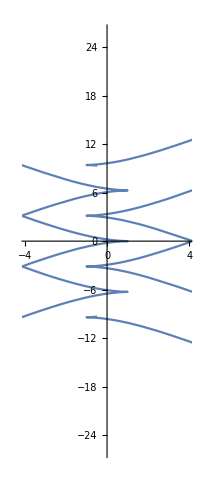

```mathematica
ParametricPlot[{-Tan[t]*Sin[t]+Cos[t],-Tan[t]+t},{t,-10,10}]
```

```mathematica
ParametricPlot3D[{-Tan[t]*Sin[t]+Cos[t],0,-Tan[t]+t},{t,-10,10}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[{x*y-x+y+z^2},{x,-2,0},{y,0,2}],{z,-5,5}]
```

```mathematica
Eigenvalues[{{0,1,0},{1,0,0},{0,0,2}}]
```

{2,-1,1}

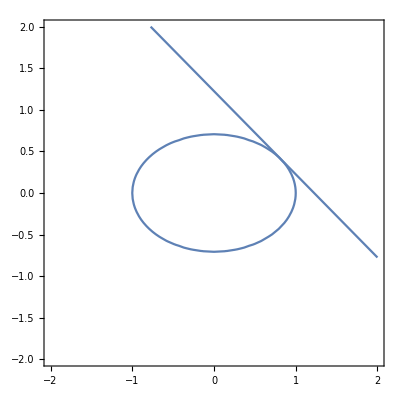

```mathematica
Show[ContourPlot[x^2+2*y^2-1==0,{x,-2,2},{y,-2,2},Axes->True],ContourPlot[x+y-(3/4)*Sqrt[8/3]==0,{x,-2,2},{y,-2,2}]]
```

```mathematica
Map[Normalize,Eigenvectors[{{-2,1,0},{1,-2,1},{0,1,-2}}]]
```

{{1/2,-1/(√2),1/2},{-1/(√2),0,1/(√2)},{1/2,1/(√2),1/2}}

```mathematica
Manipulate[
Show[
ContourPlot3D[x^2+y^2+z^2-1==0,{x,-2,2},{y,-2,2},{z,-2,2},
ContourStyle->Directive[Orange,Opacity[0.6]],
PlotPoints->100],
ContourPlot3D[2x*z+2y*z-2x^2-2y^2-2z^2-c==0,{x,-2,2},{y,-2,2},{z,-2,2},
ContourStyle->Directive[Blue,Opacity[0.6]],
PlotPoints->100]],
{c,-5,5}]
```

```mathematica
D[x^a*Exp[-x]*y^b*Exp[-y]]
```

0.0183156 2.^(a+b)

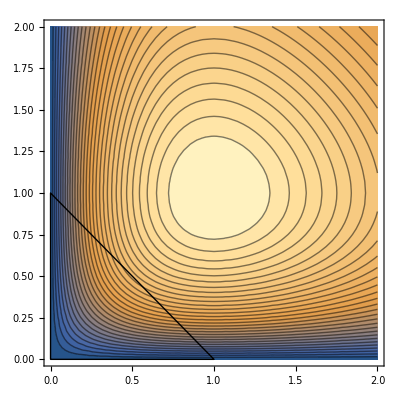

```mathematica
a=1;
b=1;
Show[ContourPlot[x^a Exp[-x] y^b Exp[-y],{x,0,2},{y,0,2},Contours->30],Graphics[Line[{{0,0},{1,0},{0,1},{0,0}}]],Axes->True]
```